### We will now attempt to find if 4-step L(κ) LMMs exist

```mathematica
ρ[a_][xi_]:=Sum[a[[i+1]] xi^i,{i,0,Length[a]-1}]
σ[b_][xi_]:=Sum[b[[i+1]] xi^i,{i,0,Length[b]-1}]
```

### Below I have combined all of the steps required to get the real part of ρ/σ:

```mathematica
BDFLikeConditions[k_]:=Module[
{orderConditions,BDFLikeOrderConditions,reducedBDFLikeOrderConditions,rhooversigma,realPartInPolar,cond,result},
orderConditions=And@@Table[Sum[Subscript[α, i] i^(q+ϵ),{i,0,k}]==q Sum[Subscript[β, i] (i)^(q+ϵ-1),{i,0,k}],{q,0,2}]/.{ 0^ϵ->1, 0^(-1+ϵ)->0,ϵ->0};
cond=Flatten@{Subscript[α, k]->1,Table[Subscript[β, i]->0,{i,0,k-1}]};
BDFLikeOrderConditions=orderConditions/.cond;
reducedBDFLikeOrderConditions=Reduce[BDFLikeOrderConditions]//ToRules;
rhooversigma[ζ_]:=(ρ[Flatten@{Table[Subscript[α, i],{i,0,k-1}],1}][ζ])/(σ[Flatten@{Table[0,{i,0,k-1}],Subscript[β, k]}][ζ])/.reducedBDFLikeOrderConditions//Simplify;
realPartInPolar=ComplexExpand@Re[rhooversigma[r Exp[ⅈ θ]]//ExpToTrig//TrigExpand]/.{Cos[θ]->c,Sin[θ]^2->1-c^2,Sin[θ]^4->(1-c^2)^2};
realPartInPolar//Simplify
]
```

### This will now give us the real part of the ρ/σ equation by simply specifying the number of steps. Note that we simplify things by replacing Sin(θ) and Cos(θ) with √(1-c^2)and c, respectively, where -1<=c<=1.

### Let us begin with 4-steps

```mathematica
realPartInPolar=BDFLikeConditions[4]
```

1/(2 r^4 β_4)(2 (-3-24 c^4-24 c r+32 c^3 r+6 r^2+r^4-12 c^2 (-2+r^2))-2 (1+8 c^4-12 c^3 r-3 r^2-c r (-9+r^2)+c^2 (-8+6 r^2)) α_3+(5+40 c^4+36 c r-48 c^3 r-7 r^2+2 c^2 (-20+7 r^2)) β_4)

### We only need the numerator, as we will only check for the case r=1 and we already know that for r>1, β_4>0

```mathematica
numer=Numerator[realPartInPolar]/.{r->1,Subscript[β, 4]->β4,Subscript[α, 3]->α3}
```

2 (4-24 c+12 c^2+32 c^3-24 c^4)-2 (-2+8 c-2 c^2-12 c^3+8 c^4) α3+(-2+36 c-26 c^2-48 c^3+40 c^4) β4

```mathematica
a=Reduce[β4>0&&ForAll[c,-1<=c<=1,numer>=0],{α3,β4},Reals]
```

(α3==1/5 (-4-√21)&&β4==1/21 (29+2 (-4-√21))-1/21 √(1-8/5 (-4-√21)-1/5 (-4-√21)^2))||(1/5 (-4-√21)<α3≤-8/5&&1/21 (29+10 α3)-1/21 √(1-8 α3-5 α3^2)≤β4≤1/21 (29+10 α3)+1/21 √(1-8 α3-5 α3^2))||(-8/5<α3≤-4/5&&1/35 (36+10 α3)≤β4≤1/21 (29+10 α3)+1/21 √(1-8 α3-5 α3^2))||(-4/5<α3≤0&&1/3 (4+2 α3)≤β4≤1/21 (29+10 α3)+1/21 √(1-8 α3-5 α3^2))||(0<α3<1/5 (-4+√21)&&1/21 (29+10 α3)-1/21 √(1-8 α3-5 α3^2)≤β4≤1/21 (29+10 α3)+1/21 √(1-8 α3-5 α3^2))||(α3==1/5 (-4+√21)&&β4==1/21 (29+2 (-4+√21))-1/21 √(1-8/5 (-4+√21)-1/5 (-4+√21)^2))

#### Plotting the region where this is holds true

```mathematica
a/.α3->-2/41 (18+11 √2)//Simplify
```

β4>0&&220 √2+√(2169-704 √2)+861 β4≥829&&220 √2+861 β4≤829+√(2169-704 √2)

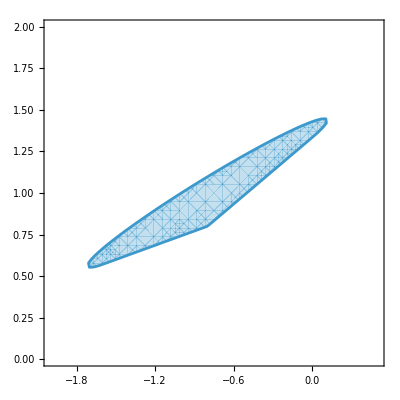

```mathematica
plt=RegionPlot[a,{α3,-2,1/2},{β4,0,2}]
```

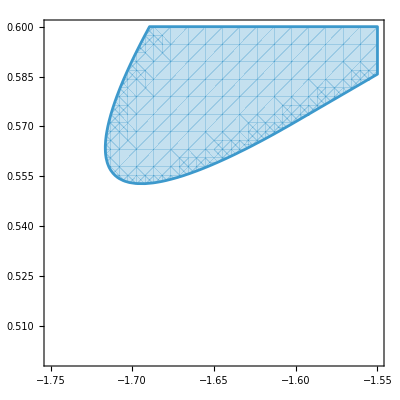

```mathematica
plt1=RegionPlot[a,{α3,-1.75,-1.55},{β4,.5,.6}]
```

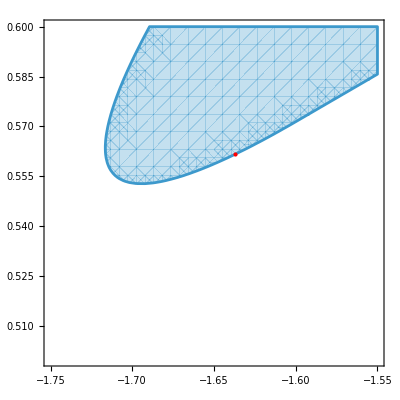

```mathematica
Show[plt1,Graphics[{Red,PointSize[Large],Point[{-2/41 (18+11 √2),-4/41 (-10+3 √2)}]}]]
```

#### Let’s now make a 3D plot where z = Error Constant

```mathematica
c3special[α_,β_]:=Module[
{a,b,sum},
a={-3-α+(5 β)/2,8+3 α-6 β,-6-3 α+(7 β)/2,α,1};
b={0,0,0,0,β};
sum=Abs[1/(σ[b][1])Sum[(j^3 a[[j+1]])/(3!)-(j^(3-1)b[[j+1]])/((3-1)!),{j,0,Length[a]-1}]];
sum
]
```

```mathematica
c3special[α,β]//Simplify
```

Abs[-13/3+(4+α)/β]

```mathematica
c4[a_,b_]:=1/(σ[b][1])Sum[(j^4 a[[j+1]])/(4!)-(j^(4-1)b[[j+1]])/((4-1)!),{j,0,Length[a]-1}]
```

```mathematica
c4[{-2,9,-18,11},{0,0,0,6}]
```

-1/4

```mathematica
Plot3D[c3special[α,β],{α,1/5 (-4-√21),1/5 (-4+√21)},{β,1/21 (29+2 (-4-√21))-1/21 √(1-8/5 (-4-√21)-1/5 (-4-√21)^2),1/21 (29+2 (-4+√21))-1/21 √(1-8/5 (-4+√21)-1/5 (-4+√21)^2)},RegionFunction->Function[{α,β,z},Evaluate[a/. {α3->α,β4->β}]],AxesLabel->{"α_3","β_4","Error"},PlotPoints->50,MaxRecursion->2]
```

-Graphics3D-

#### We now evaluate the smallest possible error constant

```mathematica
minPoint=Minimize[{c3special[α3,β4],a},{α3,β4}]//Simplify
```

{5/6-1/(√2),{α3→-2/41 (18+11 √2),β4→-4/41 (-10+3 √2)}}

```mathematica
c3special[-2/41 (18+11 √2),-4/41 (-10+3 √2)]//Simplify
```

-5/6+1/(√2)

```mathematica
N[-5/6+1/(√2)]
```

-0.126227

#### Note that 5/6-1/(√2)<1/6, which is the smallest possible error constant for a BDF-Like 3-step method

```mathematica
N[5/6-1/(√2)]
```

0.126227

```mathematica
N[1/6]
```

0.166667

#### We now derive the rest of the α-coefficients to make the resulting LMM:

```mathematica
{-3-α+(5 β)/2,8+3 α-6 β,-6-3 α+(7 β)/2,α,1}/.{α->-2/41 (18+11 √2),β->-4/41 (-10+3 √2)}//Simplify
```

{1/41 (13-8 √2),2/41 (-10+3 √2),2/41 (1+12 √2),-2/41 (18+11 √2),1}

```mathematica
Abs[xi/.NSolve[ρ[{1/41 (13-8 √2),2/41 (-10+3 √2),2/41 (1+12 √2),-2/41 (18+11 √2),1}][xi]==0,xi]]
```

{0.372557,0.372557,0.296322,1.}

#### We test for r>1

```mathematica
specialz[r_,θ_]:=ρ[{1/41 (13-8 √2),2/41 (-10+3 √2),2/41 (1+12 √2),-2/41 (18+11 √2),1}][r Exp[I θ]]/σ[{0,0,0,0,-4/41 (-10+3 √2)}][r Exp[I θ]]
```

```mathematica
Manipulate[ParametricPlot[{Re[specialz[r,θ]],Im[specialz[r,θ]]},{θ,0,2Pi},PlotRange->{{-5,7},{-5,5}}],{r,1,10}]
```

#### Testing for all r>1

```mathematica
expr=Numerator[realPartInPolar]/.{Subscript[α, 3]->-2/41 (18+11 √2),Subscript[β, 4]->-4/41 (-10+3 √2)}//Simplify
```

-2/41 (-13+8 √2+8 (-13+8 √2) c^4+8 (10-3 √2) c^3 r+(2+24 √2) r^2-41 r^4+2 c r (-30+9 √2+(18+11 √2) r^2)-4 c^2 (-26+16 √2+(1+12 √2) r^2))

```mathematica
Reduce[ForAll[{r,c},r>1&&-1<=c<=1,expr>=0],Reals]
```

True

### Let’s expand into 5 steps

```mathematica
realPartInPolar=BDFLikeConditions[5]//FullSimplify
```

1/(2 r^5 β_5)(-2 (16 c^5-3 r-24 c^4 r+r^3+c (5-9 r^2)-2 c^2 r (-12+r^2)+4 c^3 (-5+3 r^2)) α_3+2 (-6 c (5-20 c^2+16 c^4)+15 (1-8 c^2+8 c^4) r+10 c (3-4 c^2) r^2+r^5+(8 r+c (-15+60 c^2-48 c^4+64 c (-1+c^2) r+6 (3-4 c^2) r^2+r^4)) α_4)+(7 c (5-20 c^2+16 c^4)-16 (1-8 c^2+8 c^4) r+9 c (-3+4 c^2) r^2) β_5)

#### Using r = 1

```mathematica
realPartInPolar/.{r->1,Subscript[β, 5]->β5,Subscript[α, 3]->α3,Subscript[α, 4]->α4}//Simplify
```

(2 (-1+c)^2 (8+α3+4 α4-4 c^3 (12+2 α3+6 α4-7 β5)-4 c^2 (9+α3+4 α4-6 β5)+2 c (8+2 α3+5 α4-3 β5)-4 β5))/β5

#### Again, we will only look at the numerator

```mathematica
numer5=Numerator[realPartInPolar]/.{r->1,Subscript[β, 5]->β5,Subscript[α, 3]->α3,Subscript[α, 4]->α4}//Simplify
```

-4 (-1+c)^2 (-8-α3-4 α4+4 c^3 (12+2 α3+6 α4-7 β5)+4 c^2 (9+α3+4 α4-6 β5)-2 c (8+2 α3+5 α4-3 β5)+4 β5)

```mathematica
Clear[a]
```

```mathematica
a=Reduce[β5>0&&ForAll[c,-1<=c<1,numer5>=0],{α3,α4,β4},Reals]//Simplify;
```

#### Plotting the region

```mathematica
Clear[plt1]
```

```mathematica
plt1=Quiet@RegionPlot3D[a,{α3,-2,2},{α4,-2,2},{β5,0.001,4},AxesLabel->{"a3","a4","b5"},PlotPoints->40]
```

-Graphics3D-

```mathematica
{α3->1.118033661811562,α4->-1.7342033307939797,β5->0.5413559293342249}
```

```mathematica
Show[plt1,Graphics3D[{Red,Sphere[{(√5)/2,1/44 (-45-14 √5),-5/44 (-7+√5)},1/20]}]]
```

-Graphics3D-

#### Deriving the error constant equation for this case:

```mathematica
Abs[1/(σ[{0,0,0,0,0,Subscript[β, 5]}][1])Sum[(j^3{Subscript[α, 0],Subscript[α, 1],Subscript[α, 2],Subscript[α, 3],Subscript[α, 4],1}[[j+1]])/(3!)-(j^(3-1){0,0,0,0,0,Subscript[β, 5]}[[j+1]])/((3-1)!),{j,0,Length[{Subscript[α, 0],Subscript[α, 1],Subscript[α, 2],Subscript[α, 3],Subscript[α, 4],1}]-1}]]/.{Subscript[α, 2]->-10-3 Subscript[α, 3]-6 Subscript[α, 4]+(9 Subscript[β, 5])/2,Subscript[α, 1]->15+3 Subscript[α, 3]+8 Subscript[α, 4]-8 Subscript[β, 5],Subscript[α, 0]->-6-Subscript[α, 3]-3 Subscript[α, 4]+(7 Subscript[β, 5])/2}//Simplify
```

1/6 Abs[(60+6 α_3+24 α_4-47 β_5)/β_5]

#### Checking each section of a

```mathematica
Length[a]
```

12

```mathematica
Reduce[a[[10]],{α3,α4,β5},Reals]//Simplify
```

$Aborted

```mathematica
NMinimize[{1/6 Abs[(60+6 α3+24 α4-47 β5)/β5],a[[10]]},{α3,α4,β5}]
```

NMinimize::nnum: The function value Indeterminate is not a number at {α3,α4,β5} = {1.12728,-1.45343,0.678726}.

NMinimize[{1/6 Abs[(60+6 α3+24 α4-47 β5)/β5],α3==Root[96-224 β5+120 β5^2-8 β5^3+(4-56 β5+61 β5^2) #1+(-32+52 β5) #1^2+4 #1^3&,3]&&α4==Root[163200+120080 α3+33328 α3^2+4144 α3^3+196 α3^4-350080 β5-191616 α3 β5-35112 α3^2 β5-2156 α3^3 β5+281988 β5^2+102060 α3 β5^2+9261 α3^2 β5^2-101088 β5^3-18144 α3 β5^3+13608 β5^4+(349440+193088 α3+35832 α3^2+2240 α3^3-561048 β5-204900 α3 β5-18816 α3^2 β5+300672 β5^2+54432 α3 β5^2-53784 β5^3) #1+(280612+103584 α3+9648 α3^2-299712 β5-54816 α3 β5+80136 β5^2) #1^2+(100192+18544 α3-53384 β5) #1^3+13424 #1^4&,1]&&(9925/14623<β5<5/3||5/3<β5<||<β5<9925/14623)},{α3,α4,β5}]

```mathematica
FindInstance[{1/6 Abs[(60+6 α3+24 α4-47 β5)/β5]<=1/3-1/(2 √5),a[[11]]},{α3,α4,β5}]
```

{}

```mathematica
FindMinimum[{1/6 Abs[(60+6 α3+24 α4-47 β5)/β5],a[[10]]&&1/6 Abs[(60+6 α3+24 α4-47 β5)/β5]<=1/3-1/(2 √5)},{α3,α4,β5}]
```

FindMinimum::nrlnum: The function value {-1.15249+0. ⅈ,-1.66098-0.118856 ⅈ} is not a list of real numbers with dimensions {2} at {α3,α4,β5} = {0.999994,1.,1.56787}.

FindMinimum::nrlnum: The function value {-1.49781+0. ⅈ,-1.42774-0.133615 ⅈ} is not a list of real numbers with dimensions {2} at {α3,α4,β5} = {0.999994,1.,1.80779}.

Experimental`NumericalFunction::nrlnum: The function value {-0.00176675+0. ⅈ,-0.022587-0.0181031 ⅈ,-0.0645642+0. ⅈ} is not a list of real numbers with dimensions {3} at {α3,α4,β5} = {1.28619,-1.73101,0.569541}.

Experimental`NumericalFunction::nrlnum: The function value {-0.00175897+0. ⅈ,-0.0225846-0.0181027 ⅈ,-0.0645779+0. ⅈ} is not a list of real numbers with dimensions {3} at {α3,α4,β5} = {1.28619,-1.73101,0.569541}.

Experimental`NumericalFunction::nrlnum: The function value {-0.00160975+0. ⅈ,-0.0225378-0.0180951 ⅈ,-0.0648399+0. ⅈ} is not a list of real numbers with dimensions {3} at {α3,α4,β5} = {1.28604,-1.73101,0.569541}.

General::stop: Further output of Experimental`NumericalFunction::nrlnum will be suppressed during this calculation.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 500 iterations.

{0.0709656,{α3→1.30425,α4→-1.70039,β5→0.56965}}

```mathematica
N[1/12]
```

0.0833333

#### Based on checking each part of a, this is what resulted: 1, 2, 5, 7, 9, 12 produced results between 1/12 and 1 10 and 11 did not initially produce a result, but further inquiry proved they did not have the ideal minimum All the rest produced an error greater than 1 This is visualized by the graph below:

```mathematica
lst={0.1151154430973432,0.21529934028964573,1.8268298332367785,1.8261536552102584,0.2123761544920247,2.333333333333333,0.1097265303602398,1.8843967691447912,0.5515511841671222,0,0.07096557831311784,0.13167652479415654};
```

```mathematica
indexed=MapIndexed[{#2[[1]],#1}&,lst];
```

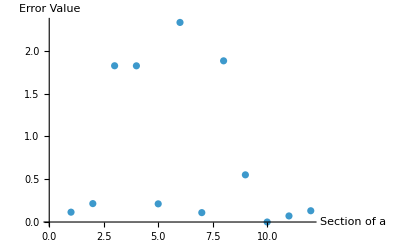

```mathematica
ListPlot[indexed,AxesLabel->{"Section of a", "Error Value"}]
```

#### If we assume that section 10 follows this trend and is not A-stable for all α_3,α_4,β_5 that satisfy that section of “a”, then a[[7]] is the best result. We analyze it below numerically and then symbolically

```mathematica
Quiet@NMinimize[{1/6 Abs[(60+6 α3+24 α4-47 β5)/β5],a[[7]]},{α3,α4,β5}]
```

{0.109727,{α3→1.11803,α4→-1.7342,β5→0.541356}}

```mathematica
Minimize[{1/6 Abs[(60+6 α3+24 α4-47 β5)/β5],a[[7]]},{α3,α4,β5}]//Simplify
```

{1/3-1/(2 √5),{α3→(√5)/2,α4→1/44 (-45-14 √5),β5→-5/44 (-7+√5)}}

```mathematica
{1/3-1/(2 √5),{α3->(√5)/2,α4->1/44 (-45-14 √5),β5->-5/44 (-7+√5)}}//N
```

{0.109727,{α3→1.11803,α4→-1.7342,β5→0.541356}}

#### Let’s check it for A-stability

```mathematica
zspecial2[r_,θ_]:=(ρ[{α0,α1,α2,α3,α4,1}][r Exp[I θ]])/(σ[{0,0,0,0,0,β5}][r Exp[I θ]])/.{α2->-10-3 α3-6 α4+(9 β5)/2,α1->15+3 α3+8 α4-8 β5,α0->-6-α3-3 α4+(7 β5)/2}/.{α3->(√5)/2,α4->1/44 (-45-14 √5),β5->-5/44 (-7+√5)}
```

```mathematica
Manipulate[ParametricPlot[{Re[zspecial2[r,θ]],Im[zspecial2[r,θ]]},{θ,0,2Pi},PlotRange->{{-5,9},{-5,5}}],{r,1,10}]
```

#### Checking for r>1

```mathematica
FindMinimum[Re[zspecial2[1,θ]],{θ,0}]
```

{0.,{θ→0.}}

```mathematica
check=Numerator[realPartInPolar]/.{Subscript[α, 3]->(√5)/2,Subscript[α, 4]->1/44 (-45-14 √5),Subscript[β, 5]->-5/44 (-7+√5)}//Simplify
```

1/44 (16 (-13+5 √5) c^5+32 (10-3 √5) c^4 r+8 c^2 r (-40+12 √5+11 √5 r^2)-4 c^3 (-65+25 √5+(25+9 √5) r^2)+4 r (10-3 √5-11 √5 r^2+22 r^4)+c (-65+25 √5+3 (25+9 √5) r^2-2 (45+14 √5) r^4))

```mathematica
Reduce[ForAll[{c,r},-1<=c<=1&&r>1,check>=0],Reals]
```

True

#### This doesn’t cross into the LHP, therefore this method is A-stable

#### Also note that 1/3-1/(2 √5)<5/6-1/(√2), the latter of which is the smallest error for 4-step BDF-like methods

#### Let’s see the alpha coefficients

```mathematica
{α0,α1,α2,α3,α4,1}/.{α2->-10-3 α3-6 α4+(9 β5)/2,α1->15+3 α3+8 α4-8 β5,α0->-6-α3-3 α4+(7 β5)/2}/.{α3->(√5)/2,α4->1/44 (-45-14 √5),β5->-5/44 (-7+√5)}//Simplify
```

{1/88 (-13+5 √5),1/22 (10-3 √5),1/88 (-25-9 √5),(√5)/2,1/44 (-45-14 √5),1}

```mathematica
Abs[xi/.NSolve[ρ[{1/88 (-13+5 √5),1/22 (10-3 √5),1/88 (-25-9 √5),(√5)/2,1/44 (-45-14 √5),1}][xi]==0,xi]]
```

{0.438102,0.438102,0.32823,0.32823,1.}

### Let’s now compare the errors of each step to each other

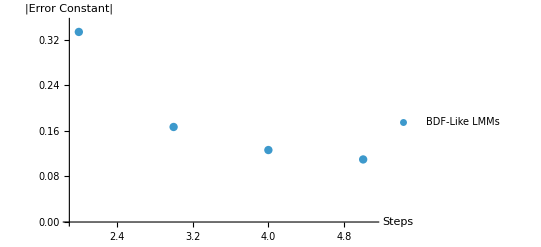

```mathematica
plt=ListPlot[{{2,1/3},{3,1/6},{4,5/6-1/(√2)},{5,1/3-1/(2 √5)}},AxesLabel->{"Steps","|Error Constant|"},PlotStyle->{{PointSize[.015]},Red},PlotLegends->{"BDF-Like LMMs"},PlotRange->{{1.9,5.1},{0.35,0}}]
```

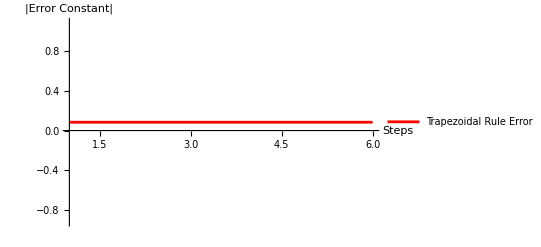

```mathematica
plt1 = Plot[1/12,{x,1,6},AxesLabel->{"Steps","|Error Constant|"},PlotStyle->Red,PlotLegends->{"Trapezoidal Rule Error"},PlotRange->{{1,5.1},{0.35,0}}]
```

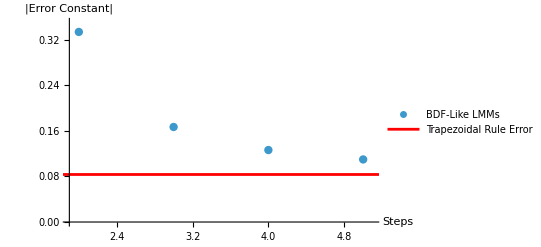

```mathematica
plt2=Show[plt,plt1]
```

```mathematica
f[n_]:=Piecewise[{{1/3,n==2},{1/6,n==3},{5/6-1/Sqrt[2],n==4},{1/3-1/(2 Sqrt[5]),n==5}}]
```

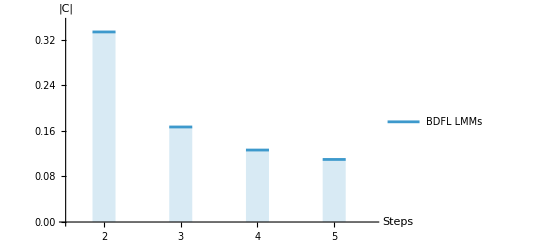

```mathematica
plt5=DiscretePlot[f[n],{n,2,5},AxesLabel->{"Steps","|C|"},ExtentSize->.3,PlotRange->{{1.5,5.5},{0,0.35}},PlotLegends->{"BDFL LMMs"},Ticks->{{2,3,4,5},Automatic},ImageSize->400]
```

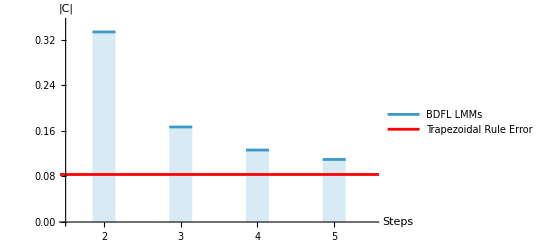

```mathematica
plt2=Show[plt5,plt1]
```

```mathematica
SetDirectory[$UserDocumentsDirectory]
```

C:\Users\Tyler Jensen\OneDrive - Brigham Young University\Documents

```mathematica
SetDirectory["C:\\Users\\Tyler Jensen\\Downloads"]
```

C:\Users\Tyler Jensen\Downloads

```mathematica
Export["error_to_step.pdf",Rasterize[plt2]]
```

error_to_step.pdf